```mathematica
(*CHARLIE 1 Trusted*)
```

```mathematica
σ[0]=PauliMatrix[0];
σ0=PauliMatrix[0];
σ[1]=PauliMatrix[1];
σ[2]=PauliMatrix[2];
σ[3]=PauliMatrix[3];
u=({{1}, {0}});
d=({{0}, {1}});
ρGHZ=(*1/2*)Simplify[((Cos[θ] KroneckerProduct[u,u,u]+Sin[θ]KroneckerProduct[d,d,d]).ConjugateTranspose[(Cos[θ] KroneckerProduct[u,u,u]+Sin[θ]KroneckerProduct[d,d,d])]),0<θ<π/2];
x1[i1_,-1]:=1/2(σ0-σ[i1]);
x1[i1_,1]:=1/2(σ0+σ[i1]);
y2[j2_,-1]:=1/2(σ0-σ[j2]);
y2[j2_,1]:=1/2(σ0+σ[j2]);
z31[k3_,-1]:=1/2(σ0-σ[k3]);
z31[k3_,1]:=1/2(σ0+σ[k3]);
P1[j2_,k3_,b1_,c1_]:=Tr[KroneckerProduct[σ0,y2[j2,b1],z31[k3,c1]].ρGHZ];
Cqq[j2_,k3_]:=Sum[b1*c1*P1[j2,k3,b1,c1],{b1,-1,1,2},{c1,-1,1,2}];
P2[i1_,j2_,a1_,b1_]:=Tr[KroneckerProduct[x1[i1,a1],y2[j2,b1],σ0].ρGHZ];
C2qq[i1_,j2_]:=Sum[a1*b1*P2[i1,j2,a1,b1],{a1,-1,1,2},{b1,-1,1,2}];P3[i1_,k3_,a1_,c1_]:=Tr[KroneckerProduct[x1[i1,a1],σ0,z31[k3,c1]].ρGHZ];
C3qq[i1_,k3_]:=Sum[a1*c1*P3[i1,k3,a1,c1],{a1,-1,1,2},{c1,-1,1,2}];
P[i1_,j2_,k3_,a1_,b1_,c1_]:=Tr[KroneckerProduct[x1[i1,a1],y2[j2,b1],z31[k3,c1]].ρGHZ];
Cq[i1_,j2_,k3_]:=Sum[a1*b1*c1*P[i1,j2,k3,a1,b1,c1],{a1,-1,1,2},{b1,-1,1,2},{c1,-1,1,2}];
Simplify[1-α(C2qq[3,3]+C3qq[3,3]+Cqq[3,3])-β(Cq[1,1,1]-Cq[1,2,2]-Cq[2,1,2]-Cq[2,2,1])]
```

1-3 α-8 β Cos[θ] Sin[θ]

```mathematica
α=0.1831;β=0.2582;
Simplify[1-3 α-8 β Cos[θ] Sin[θ]]
Plot[1-3 α-8 β Cos[θ] Sin[θ],{θ,0,π/2}]
Clear[α,β]
```

0.4507-2.0656 Cos[θ] Sin[θ]

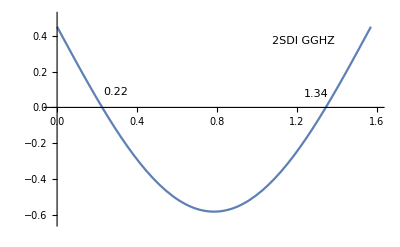

```mathematica
α=0.1831;β=0.2582;
NMinimize[{1-α λ1 Cos[θ2[3]] Cos[θ31[3]]-α Cos[θ1[3]] (Cos[θ2[3]]+λ1 Cos[θ31[3]])-β λ1 Cos[ϕ1[1]] Cos[ϕ2[1]] Cos[ϕ31[1]] Sin[θ1[1]] Sin[θ2[1]] Sin[θ31[1]]+β λ1 Cos[ϕ1[2]] Cos[ϕ2[2]] Cos[ϕ31[1]] Sin[θ1[2]] Sin[θ2[2]] Sin[θ31[1]]+β λ1 Cos[ϕ1[2]] Cos[ϕ2[1]] Cos[ϕ31[2]] Sin[θ1[2]] Sin[θ2[1]] Sin[θ31[2]]+β λ1 Cos[ϕ1[1]] Cos[ϕ2[2]] Cos[ϕ31[2]] Sin[θ1[1]] Sin[θ2[2]] Sin[θ31[2]]+β λ1 Cos[ϕ31[1]] Sin[θ1[1]] Sin[θ2[1]] Sin[θ31[1]] Sin[ϕ1[1]] Sin[ϕ2[1]]-β λ1 Cos[ϕ31[2]] Sin[θ1[2]] Sin[θ2[1]] Sin[θ31[2]] Sin[ϕ1[2]] Sin[ϕ2[1]]-β λ1 Cos[ϕ31[2]] Sin[θ1[1]] Sin[θ2[2]] Sin[θ31[2]] Sin[ϕ1[1]] Sin[ϕ2[2]]-β λ1 Cos[ϕ31[1]] Sin[θ1[2]] Sin[θ2[2]] Sin[θ31[1]] Sin[ϕ1[2]] Sin[ϕ2[2]]+β λ1 Cos[ϕ2[1]] Sin[θ1[1]] Sin[θ2[1]] Sin[θ31[1]] Sin[ϕ1[1]] Sin[ϕ31[1]]-β λ1 Cos[ϕ2[2]] Sin[θ1[2]] Sin[θ2[2]] Sin[θ31[1]] Sin[ϕ1[2]] Sin[ϕ31[1]]+β λ1 Cos[ϕ1[1]] Sin[θ1[1]] Sin[θ2[1]] Sin[θ31[1]] Sin[ϕ2[1]] Sin[ϕ31[1]]-β λ1 Cos[ϕ1[2]] Sin[θ1[2]] Sin[θ2[2]] Sin[θ31[1]] Sin[ϕ2[2]] Sin[ϕ31[1]]-β λ1 Cos[ϕ2[2]] Sin[θ1[1]] Sin[θ2[2]] Sin[θ31[2]] Sin[ϕ1[1]] Sin[ϕ31[2]]-β λ1 Cos[ϕ2[1]] Sin[θ1[2]] Sin[θ2[1]] Sin[θ31[2]] Sin[ϕ1[2]] Sin[ϕ31[2]]-β λ1 Cos[ϕ1[2]] Sin[θ1[2]] Sin[θ2[1]] Sin[θ31[2]] Sin[ϕ2[1]] Sin[ϕ31[2]]-β λ1 Cos[ϕ1[1]] Sin[θ1[1]] Sin[θ2[2]] Sin[θ31[2]] Sin[ϕ2[2]] Sin[ϕ31[2]],0≤θ31[0]≤π/2,0≤ϕ31[0]≤π,0≤θ31[1]≤π/2,0≤ϕ31[1]≤π,0≤θ31[2]≤π/2,0≤ϕ31[2]≤π,0≤θ31[3]≤π/2,0≤ϕ31[3]≤π,0≤θ1[0]≤π/2,0≤ϕ1[0]≤π,0≤θ1[1]≤π/2,0≤ϕ1[1]≤π,0≤θ1[2]≤π/2,0≤ϕ1[2]≤π,0≤θ1[3]≤π/2,0≤ϕ1[3]≤π,0≤θ2[0]≤π/2,0≤ϕ2[0]≤π,0≤θ2[1]≤π/2,0≤ϕ2[1]≤π,0≤θ2[2]≤π/2,0≤ϕ2[2]≤π,0≤θ2[3]≤π/2,0≤ϕ2[3]≤π,0≤λ1≤1},{θ1[0],ϕ1[0],θ1[1],ϕ1[1],θ2[0],ϕ2[0],θ2[1],ϕ2[1],θ31[0],ϕ31[0],θ31[1],ϕ31[1],θ1[2],ϕ1[2],θ1[3],ϕ1[3],θ2[2],ϕ2[2],θ2[3],ϕ2[3],θ31[2],ϕ31[2],θ31[3],ϕ31[3],λ1}]
Clear[α,β]
```

```mathematica
{-0.5820999999999924,{θ1[0]->0.8752469052500946,ϕ1[0]->0.,θ1[1]->1.5707962796491564,ϕ1[1]->1.5716828974453059,θ2[0]->0.6282677383363527,ϕ2[0]->2.806405299336295,θ2[1]->1.5707962962357138,ϕ2[1]->1.9335092322978849,θ31[0]->1.1895686421098461,ϕ31[0]->2.0100649234862606,θ31[1]->1.5707962423067128,ϕ31[1]->2.777993144397754,θ1[2]->1.570796275064507,ϕ1[2]->0.0008865584907918677,θ1[3]->0.,ϕ1[3]->1.314363384147486,θ2[2]->1.5707962673948646,ϕ2[2]->0.3627129029410969,θ2[3]->1.9584226074438428*^-8,ϕ2[3]->1.6769677169551165,θ31[2]->1.5707963034287336,ϕ31[2]->1.2071968758824991,θ31[3]->1.200833536695493*^-7,ϕ31[3]->1.0477400860033823,λ1->1.}}
```

```mathematica
(*λ1=1;*)α=0.1831;β=0.2582;
θ1[1]=π/2;ϕ1[1]=0;θ2[1]=π/2;ϕ2[1]=0;θ31[1]=π/2;ϕ31[1]=0;θ1[2]=π/2;ϕ1[2]=π/2;θ1[3]=0;ϕ1[3]=0;θ2[2]=π/2;ϕ2[2]=π/2;θ2[3]=0;ϕ2[3]=0;θ31[2]=π/2;ϕ31[2]=π/2;θ31[3]=0;ϕ31[3]=0;

Simplify[1-α λ1 Cos[θ2[3]] Cos[θ31[3]]-α Cos[θ1[3]] (Cos[θ2[3]]+λ1 Cos[θ31[3]])-β λ1 Cos[ϕ1[1]] Cos[ϕ2[1]] Cos[ϕ31[1]] Sin[θ1[1]] Sin[θ2[1]] Sin[θ31[1]]+β λ1 Cos[ϕ1[2]] Cos[ϕ2[2]] Cos[ϕ31[1]] Sin[θ1[2]] Sin[θ2[2]] Sin[θ31[1]]+β λ1 Cos[ϕ1[2]] Cos[ϕ2[1]] Cos[ϕ31[2]] Sin[θ1[2]] Sin[θ2[1]] Sin[θ31[2]]+β λ1 Cos[ϕ1[1]] Cos[ϕ2[2]] Cos[ϕ31[2]] Sin[θ1[1]] Sin[θ2[2]] Sin[θ31[2]]+β λ1 Cos[ϕ31[1]] Sin[θ1[1]] Sin[θ2[1]] Sin[θ31[1]] Sin[ϕ1[1]] Sin[ϕ2[1]]-β λ1 Cos[ϕ31[2]] Sin[θ1[2]] Sin[θ2[1]] Sin[θ31[2]] Sin[ϕ1[2]] Sin[ϕ2[1]]-β λ1 Cos[ϕ31[2]] Sin[θ1[1]] Sin[θ2[2]] Sin[θ31[2]] Sin[ϕ1[1]] Sin[ϕ2[2]]-β λ1 Cos[ϕ31[1]] Sin[θ1[2]] Sin[θ2[2]] Sin[θ31[1]] Sin[ϕ1[2]] Sin[ϕ2[2]]+β λ1 Cos[ϕ2[1]] Sin[θ1[1]] Sin[θ2[1]] Sin[θ31[1]] Sin[ϕ1[1]] Sin[ϕ31[1]]-β λ1 Cos[ϕ2[2]] Sin[θ1[2]] Sin[θ2[2]] Sin[θ31[1]] Sin[ϕ1[2]] Sin[ϕ31[1]]+β λ1 Cos[ϕ1[1]] Sin[θ1[1]] Sin[θ2[1]] Sin[θ31[1]] Sin[ϕ2[1]] Sin[ϕ31[1]]-β λ1 Cos[ϕ1[2]] Sin[θ1[2]] Sin[θ2[2]] Sin[θ31[1]] Sin[ϕ2[2]] Sin[ϕ31[1]]-β λ1 Cos[ϕ2[2]] Sin[θ1[1]] Sin[θ2[2]] Sin[θ31[2]] Sin[ϕ1[1]] Sin[ϕ31[2]]-β λ1 Cos[ϕ2[1]] Sin[θ1[2]] Sin[θ2[1]] Sin[θ31[2]] Sin[ϕ1[2]] Sin[ϕ31[2]]-β λ1 Cos[ϕ1[2]] Sin[θ1[2]] Sin[θ2[1]] Sin[θ31[2]] Sin[ϕ2[1]] Sin[ϕ31[2]]-β λ1 Cos[ϕ1[1]] Sin[θ1[1]] Sin[θ2[2]] Sin[θ31[2]] Sin[ϕ2[2]] Sin[ϕ31[2]]]

Clear[θ1[0],ϕ1[0],θ1[1],ϕ1[1],θ2[0],ϕ2[0],θ2[1],ϕ2[1],λ1,θ31[0],ϕ31[0],θ31[1],ϕ31[1],θ1[2],ϕ1[2],θ1[3],ϕ1[3],θ2[2],ϕ2[2],θ2[3],ϕ2[3],θ31[2],ϕ31[2],θ31[3],ϕ31[3],α,β]
```

0.8169-1.399 λ1

Clear::ssym: θ1[0] is not a symbol or a string.

Clear::ssym: ϕ1[0] is not a symbol or a string.

Clear::ssym: θ1[1] is not a symbol or a string.

General::stop: Further output of Clear :: ssym will be suppressed during this calculation.

```mathematica
0.8169/1.399
```

0.583917

```mathematica
(*CHARLIE 2 Come in picture*)
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
u=({{1},{0}});
d=({{0},{1}});
ρGHZ=1/2 ((KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d]).ConjugateTranspose[(KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d])]);
x1[i1_,a1_]:=1/2 (σ0+a1*(Sin[θ1[i1]]*Cos[ϕ1[i1]]*σ1+Sin[θ1[i1]]*Sin[ϕ1[i1]]*σ2+Cos[θ1[i1]]*σ3));
y2[j2_,b1_]:=1/2 (σ0+b1*(Sin[θ2[j2]]*Cos[ϕ2[j2]]*σ1+Sin[θ2[j2]]*Sin[ϕ2[j2]]*σ2+Cos[θ2[j2]]*σ3));
(*T1[1]=λ1;T1[2]=λ1;T1[3]=1;*)
zR31[k3_,c1_]:=Sqrt[(1+(*T1[k3]*)λ1)/2] (1/2 (σ0+c1*(Sin[θ31[k3]]*Cos[ϕ31[k3]]*σ1+Sin[θ31[k3]]*Sin[ϕ31[k3]]*σ2+Cos[θ31[k3]]*σ3)))+Sqrt[(1-(*T1[k3]*)λ1)/2] (1/2 (σ0-c1*(Sin[θ31[k3]]*Cos[ϕ31[k3]]*σ1+Sin[θ31[k3]]*Sin[ϕ31[k3]]*σ2+Cos[θ31[k3]]*σ3)));
ρABC[i1_,j2_,k3_,a1_,b1_,c1_]:=((KroneckerProduct[x1[i1,a1],y2[j2,b1],zR31[k3,c1]]).ρGHZ.(KroneckerProduct[x1[i1,a1],y2[j2,b1],zR31[k3,c1]]));
ρ0BC[j2_,k3_,b1_,c1_]:=((KroneckerProduct[σ0,y2[j2,b1],zR31[k3,c1]]).ρGHZ.(KroneckerProduct[σ0,y2[j2,b1],zR31[k3,c1]]));
ρA0C[i1_,k3_,a1_,c1_]:=((KroneckerProduct[x1[i1,a1],σ0,zR31[k3,c1]]).ρGHZ.(KroneckerProduct[x1[i1,a1],σ0,zR31[k3,c1]]));
ρAB0[i1_,j2_,a1_,b1_]:=((KroneckerProduct[x1[i1,a1],y2[j2,b1],σ0]).ρGHZ.(KroneckerProduct[x1[i1,a1],y2[j2,b1],σ0]));
(*MatrixForm[ρABC[1,1,1,1,1,1]];
MatrixForm[ρ0BC[1,1,1,1]];
MatrixForm[ρA0C[1,1,1,1]];
*)
SwapParts[expr_,pos1_,pos2_]:=ReplacePart[#,#,{pos1,pos2},{pos2,pos1}]&[expr]
TraceSystem[D_,s_]:=(Qubits=Reverse[Sort[s]];
TrkM=D;
z=(Dimensions[Qubits][[1]]+1);
For[q=1,q<z,q++,n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];],For[j=0,j<(n-k),j++,b={0};
For[i=1,i<2^n+1,i++,If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1&&Count[b,i]==0,Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)}];
M=M[[perm,perm]];]];
TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];]];]];Return[TrkM]);
```

```mathematica
(*α=0.1831;β=0.2582;*)
ρBC[i1_,j2_,k3_,a1_,b1_,c1_]:=Simplify[TraceSystem[ρABC[i1,j2,k3,a1,b1,c1],{1}]];
ρC[i1_,j2_,k3_,a1_,b1_,c1_]:=Simplify[TraceSystem[ρBC[i1,j2,k3,a1,b1,c1],{1}]];
ρ1BC[j2_,k3_,b1_,c1_]:=Simplify[TraceSystem[ρ0BC[j2,k3,b1,c1],{1}]];
ρ1C[j2_,k3_,b1_,c1_]:=Simplify[TraceSystem[ρ1BC[j2,k3,b1,c1],{1}]];
ρ2BC[i1_,k3_,a1_,c1_]:=Simplify[TraceSystem[ρA0C[i1,k3,a1,c1],{1}]];
ρ2C[i1_,k3_,a1_,c1_]:=Simplify[TraceSystem[ρ2BC[i1,k3,a1,c1],{1}]];
(*T2[1]=λ2;T2[2]=λ2;T2[3]=1;*)
z32[k32_,c2_]:=(*T2[k32] *)λ2(1/2 (σ0+c2*(Sin[θ32[k32]]*Cos[ϕ32[k32]]*σ1+Sin[θ32[k32]]*Sin[ϕ32[k32]]*σ2+Cos[θ32[k32]]*σ3)))+((1-(*T2[k32]*)λ2)σ0)/2;

PC1[i1_,j2_,k3_,k32_,a1_,b1_,c2_]:=Sum[(Tr[z32[k32,c2].ρC[i1,j2,k3,a1,b1,c1]]),{c1,-1,1,2}];PC2[j2_,k3_,k32_,b1_,c2_]:=Sum[(Tr[z32[k32,c2].ρ1C[j2,k3,b1,c1]]),{c1,-1,1,2}];
PC3[i1_,k3_,k32_,a1_,c2_]:=Sum[(Tr[z32[k32,c2].ρ2C[i1,k3,a1,c1]]),{c1,-1,1,2}];
Cqq1[j2_,k3_,k32_]:=Sum[b1*c2*PC2[j2,k3,k32,b1,c2],{b1,-1,1,2},{c2,-1,1,2}];
Cqqa[j2_,k32_]:=1/3 (Cqq1[j2,1,k32]+Cqq1[j2,2,k32]+Cqq1[j2,3,k32]);
P2[i1_,j2_,a1_,b1_]:=Tr[KroneckerProduct[x1[i1,a1],y2[j2,b1],σ0].ρGHZ];
C2qq[i1_,j2_]:=Sum[a1*b1*P2[i1,j2,a1,b1],{a1,-1,1,2},{b1,-1,1,2}];
C3qq1[i1_,k3_,k32_]:=Sum[a1*c2*PC3[i1,k3,k32,a1,c2],{a1,-1,1,2},{c2,-1,1,2}];
C3qqa[i1_,k32_]:=1/3 (C3qq1[i1,1,k32]+C3qq1[i1,2,k32]+C3qq1[i1,3,k32]);
P1[i1_,j2_,k3_,k32_,a1_,b1_,c2_]:=Sum[(Tr[z32[k32,c2].ρC[i1,j2,k3,a1,b1,c1]]),{c1,-1,1,2}];
Cq1[i1_,j2_,k3_,k32_]:=Sum[a1*b1*c2*P1[i1,j2,k3,k32,a1,b1,c2],{a1,-1,1,2},{b1,-1,1,2},{c2,-1,1,2}];
Cqa[i1_,j2_,k32_]:=1/3 (Cq1[i1,j2,1,k32]+Cq1[i1,j2,2,k32]+Cq1[i1,j2,3,k32]);
```

```mathematica
λ1=0.583917;
θ1[1]=π/2;ϕ1[1]=0;θ2[1]=π/2;ϕ2[1]=0;θ31[1]=π/2;ϕ31[1]=0;θ1[2]=π/2;ϕ1[2]=π/2;θ1[3]=0;ϕ1[3]=0;θ2[2]=π/2;ϕ2[2]=π/2;θ2[3]=0;ϕ2[3]=0;θ31[2]=π/2;ϕ31[2]=π/2;θ31[3]=0;ϕ31[3]=0;
θ32[1]=π/2;ϕ32[1]=0;θ32[2]=π/2;ϕ32[2]=π/2;θ32[3]=0;ϕ32[3]=0;
α=0.1831;β=0.2582;
Simplify[1-α(C2qq[3,3]+C3qqa[3,3]+Cqqa[3,3])-β(Cqa[1,1,1]-Cqa[1,2,2]-Cqa[2,1,2]-Cqa[2,2,1])]
Clear[λ1,λ2]
```

(0.8169+0. ⅈ)-(1.22348+0. ⅈ) λ2

```mathematica
0.8169/1.22348
```

0.667686

```mathematica
(*CHARLIE 3 Come in picture*)
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
u=({{1}, {0}});
d=({{0}, {1}});
ρGHZ=1/2(( KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d]).ConjugateTranspose[( KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d])]);
x1[i1_,a1_]:=1/2(σ0+a1*(Sin[θ1[i1]]*Cos[ϕ1[i1]]*σ1+Sin[θ1[i1]]*Sin[ϕ1[i1]]*σ2+Cos[θ1[i1]]*σ3));
y2[j2_,b1_]:=1/2(σ0+b1*(Sin[θ2[j2]]*Cos[ϕ2[j2]]*σ1+Sin[θ2[j2]]*Sin[ϕ2[j2]]*σ2+Cos[θ2[j2]]*σ3));
(*T1[1]=λ1;T1[2]=λ1;T1[3]=1;*)
z31[k31_,c1_]:=Sqrt[(1+(*T1[k31]*)λ1)/2](1/2(σ0+c1*(Sin[θ31[k31]]*Cos[ϕ31[k31]]*σ1+Sin[θ31[k31]]*Sin[ϕ31[k31]]*σ2+Cos[θ31[k31]]*σ3))) +Sqrt[(1-(*T1[k31]*)λ1)/2](1/2(σ0-c1*(Sin[θ31[k31]]*Cos[ϕ31[k31]]*σ1+Sin[θ31[k31]]*Sin[ϕ31[k31]]*σ2+Cos[θ31[k31]]*σ3)));
(*T2[1]=λ2;T2[2]=λ2;T2[3]=1;*)
z32[k32_,c2_]:=Sqrt[(1+(*T2[k32]*)λ2)/2](1/2(σ0+c2*(Sin[θ32[k32]]*Cos[ϕ32[k32]]*σ1+Sin[θ32[k32]]*Sin[ϕ32[k32]]*σ2+Cos[θ32[k32]]*σ3))) +Sqrt[(1-(*T2[k32]*)λ2)/2](1/2(σ0-c2*(Sin[θ32[k32]]*Cos[ϕ32[k32]]*σ1+Sin[θ32[k32]]*Sin[ϕ32[k32]]*σ2+Cos[θ32[k32]]*σ3)));
ρABC1[i1_,j2_,k31_,a1_,b1_,c1_]:=((KroneckerProduct[x1[i1,a1],y2[j2,b1],z31[k31,c1]]).ρGHZ.(KroneckerProduct[x1[i1,a1],y2[j2,b1],z31[k31,c1]]));
ρABC2[i1_,j2_,k31_,k32_,a1_,b1_,c1_,c2_]:=((KroneckerProduct[σ0,σ0,z32[k32,c2]]).ρABC1[i1,j2,k31,a1,b1,c1].(KroneckerProduct[σ0,σ0,z32[k32,c2]]));
ρ0BC1[j2_,k31_,b1_,c1_]:=((KroneckerProduct[σ0,y2[j2,b1],z31[k31,c1]]).ρGHZ.(KroneckerProduct[σ0,y2[j2,b1],z31[k31,c1]]));
ρ0BC2[j2_,k31_,k32_,b1_,c1_,c2_]:=((KroneckerProduct[σ0,σ0,z32[k32,c2]]).ρ0BC1[j2,k31,b1,c1].(KroneckerProduct[σ0,σ0,z32[k32,c2]]));
ρA0C1[i1_,k31_,a1_,c1_]:=((KroneckerProduct[x1[i1,a1],σ0,z31[k31,c1]]).ρGHZ.(KroneckerProduct[x1[i1,a1],σ0,z31[k31,c1]]));
ρA0C2[i1_,k31_,k32_,a1_,c1_,c2_]:=((KroneckerProduct[σ0,σ0,z32[k32,c2]]).ρA0C1[i1,k31,a1,c1].(KroneckerProduct[σ0,σ0,z32[k32,c2]]));
ρAB0[i1_,j2_,a1_,b1_]:=((KroneckerProduct[x1[i1,a1],y2[j2,b1],σ0]).ρGHZ.(KroneckerProduct[x1[i1,a1],y2[j2,b1],σ0]));
```

```mathematica
SwapParts[expr_,pos1_,pos2_]:=ReplacePart[#,#,{pos1,pos2},{pos2,pos1}]&[expr]
TraceSystem[D_,s_]:=(Qubits=Reverse[Sort[s]];
TrkM=D;
z=(Dimensions[Qubits][[1]]+1);
For[q=1,q<z,q++,n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];],For[j=0,j<(n-k),j++,b={0};
For[i=1,i<2^n+1,i++,If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1&&Count[b,i]==0,Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)}];
M=M[[perm,perm]];]];
TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];]];]];Return[TrkM]);
```

```mathematica
ρBC2[i1_,j2_,k31_,k32_,a1_,b1_,c1_,c2_]:=Simplify[TraceSystem[ρABC2[i1,j2,k31,k32,a1,b1,c1,c2],{1}]];
ρC2[i1_,j2_,k31_,k32_,a1_,b1_,c1_,c2_]:=Simplify[TraceSystem[ρBC2[i1,j2,k31,k32,a1,b1,c1,c2],{1}]];
ρ1BC2[j2_,k31_,k32_,b1_,c1_,c2_]:=Simplify[TraceSystem[ρ0BC2[j2,k31,k32,b1,c1,c2],{1}]];
ρ1C2[j2_,k31_,k32_,b1_,c1_,c2_]:=Simplify[TraceSystem[ρ1BC2[j2,k31,k32,b1,c1,c2],{1}]];
ρ2BC2[i1_,k31_,k32_,a1_,c1_,c2_]:=Simplify[TraceSystem[ρA0C2[i1,k31,k32,a1,c1,c2],{1}]];
ρ2C2[i1_,k31_,k32_,a1_,c1_,c2_]:=Simplify[TraceSystem[ρ2BC2[i1,k31,k32,a1,c1,c2],{1}]];
(*z32[k32_,c2_]:=λ2 (1/2 (σ0+c2*(Sin[θ32[k32]]*Cos[ϕ32[k32]]*σ1+Sin[θ32[k32]]*Sin[ϕ32[k32]]*σ2+Cos[θ32[k32]]*σ3)))+(1-λ2)/2 σ0;*)
(*T3[1]=λ3;T3[2]=λ3;T3[3]=1;*)
z33[k33_,c3_]:=(*T3[k33] *)λ3(1/2 (σ0+c3*(Sin[θ33[k33]]*Cos[ϕ33[k33]]*σ1+Sin[θ33[k33]]*Sin[ϕ33[k33]]*σ2+Cos[θ33[k33]]*σ3)))+((1-(*T3[k33]*)λ3)σ0)/2;
P22[i1_,j2_,k31_,k32_,k33_,a1_,b1_,c3_]:=Sum[(Tr[z33[k33,c3].ρC2[i1,j2,k31,k32,a1,b1,c1,c2]]),{c1,-1,1,2},{c2,-1,1,2}];
Cq2[i1_,j2_,k31_,k32_,k33_]:=Sum[a1*b1*c3*P22[i1,j2,k31,k32,k33,a1,b1,c3],{a1,-1,1,2},{b1,-1,1,2},{c3,-1,1,2}];
Cqa2[i1_,j2_,k33_]:=1/9 (Cq2[i1,j2,1,1,k33]+Cq2[i1,j2,1,2,k33]+Cq2[i1,j2,1,3,k33]+Cq2[i1,j2,2,1,k33]+Cq2[i1,j2,2,2,k33]+Cq2[i1,j2,2,3,k33]+Cq2[i1,j2,3,1,k33]+Cq2[i1,j2,3,2,k33]+Cq2[i1,j2,3,3,k33]);
PC22[j2_,k31_,k32_,k33_,b1_,c3_]:=Sum[(Tr[z33[k33,c3].ρ1C2[j2,k31,k32,b1,c1,c2]]),{c1,-1,1,2},{c2,-1,1,2}];
PC32[i1_,k31_,k32_,k33_,a1_,c3_]:=Sum[(Tr[z33[k33,c3].ρ2C2[i1,k31,k32,a1,c1,c2]]),{c1,-1,1,2},{c2,-1,1,2}];
Cqq21[j2_,k31_,k32_,k33_]:=Sum[b1*c3*PC22[j2,k31,k32,k33,b1,c3],{b1,-1,1,2},{c3,-1,1,2}];
Cqq2a[j2_,k33_]:=1/9 (Cqq21[j2,1,1,k33]+Cqq21[j2,1,2,k33]+Cqq21[j2,1,3,k33]+Cqq21[j2,2,1,k33]+Cqq21[j2,2,2,k33]+Cqq21[j2,2,3,k33]+Cqq21[j2,3,1,k33]+Cqq21[j2,3,2,k33]+Cqq21[j2,3,3,k33]);
P2[i1_,j2_,a1_,b1_]:=Tr[KroneckerProduct[x1[i1,a1],y2[j2,b1],σ0].ρGHZ];
C2qq[i1_,j2_]:=Sum[a1*b1*P2[i1,j2,a1,b1],{a1,-1,1,2},{b1,-1,1,2}];
C3qq12[i1_,k31_,k32_,k33_]:=Sum[a1*c3*PC32[i1,k31,k32,k33,a1,c3],{a1,-1,1,2},{c3,-1,1,2}];
C3qq2a[i1_,k33_]:=1/9 (C3qq12[i1,1,1,k33]+C3qq12[i1,1,2,k33]+C3qq12[i1,1,3,k33]+C3qq12[i1,2,1,k33]+C3qq12[i1,2,2,k33]+C3qq12[i1,2,3,k33]+C3qq12[i1,3,1,k33]+C3qq12[i1,3,2,k33]+C3qq12[i1,3,3,k33]);
```

```mathematica
(*λ3=1;*)α=0.1831;β=0.2582;
λ2=0.667686;
  λ1=0.583917;
θ1[1]=π/2;ϕ1[1]=0;θ2[1]=π/2;ϕ2[1]=0;θ31[1]=π/2;ϕ31[1]=0;θ1[2]=π/2;ϕ1[2]=π/2;θ1[3]=0;ϕ1[3]=0;θ2[2]=π/2;ϕ2[2]=π/2;θ2[3]=0;ϕ2[3]=0;θ31[2]=π/2;ϕ31[2]=π/2;θ31[3]=0;ϕ31[3]=0;
θ32[1]=π/2;ϕ32[1]=0;θ32[2]=π/2;ϕ32[2]=π/2;θ32[3]=0;ϕ32[3]=0;
θ33[1]=π/2;ϕ33[1]=0;θ33[2]=π/2;ϕ33[2]=π/2;θ33[3]=0;ϕ33[3]=0;
Simplify[Simplify[1-α(C2qq[3,3]+C3qq2a[3,3]+Cqq2a[3,3])-β(Cqa2[1,1,1]-Cqa2[1,2,2]-Cqa2[2,1,2]-Cqa2[2,2,1])]]
Clear[λ1,λ2,λ3]
```

(0.8169+0. ⅈ)-(1.01504+0. ⅈ) λ3

```mathematica
0.8169/1.01504
```

0.804796

```mathematica
(*CHARLIE 4 Come in picture*)
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
u=({{1}, {0}});
d=({{0}, {1}});
ρGHZ=1/2(( KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d]).ConjugateTranspose[( KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d])]);
x1[i1_,a1_]:=1/2(σ0+a1*(Sin[θ1[i1]]*Cos[ϕ1[i1]]*σ1+Sin[θ1[i1]]*Sin[ϕ1[i1]]*σ2+Cos[θ1[i1]]*σ3));
y2[j2_,b1_]:=1/2(σ0+b1*(Sin[θ2[j2]]*Cos[ϕ2[j2]]*σ1+Sin[θ2[j2]]*Sin[ϕ2[j2]]*σ2+Cos[θ2[j2]]*σ3));
(*T1[1]=λ1;T1[2]=λ1;T1[3]=1;*)
z31[k31_,c1_]:=Sqrt[(1+(*T1[k31]*)λ1)/2](1/2(σ0+c1*(Sin[θ31[k31]]*Cos[ϕ31[k31]]*σ1+Sin[θ31[k31]]*Sin[ϕ31[k31]]*σ2+Cos[θ31[k31]]*σ3))) +Sqrt[(1-(*T1[k31]*)λ1)/2](1/2(σ0-c1*(Sin[θ31[k31]]*Cos[ϕ31[k31]]*σ1+Sin[θ31[k31]]*Sin[ϕ31[k31]]*σ2+Cos[θ31[k31]]*σ3)));
(*T2[1]=λ2;T2[2]=λ2;T2[3]=1;*)
z32[k32_,c2_]:=Sqrt[(1+(*T2[k32]*)λ2)/2](1/2(σ0+c2*(Sin[θ32[k32]]*Cos[ϕ32[k32]]*σ1+Sin[θ32[k32]]*Sin[ϕ32[k32]]*σ2+Cos[θ32[k32]]*σ3))) +Sqrt[(1-(*T2[k32]*)λ2)/2](1/2(σ0-c2*(Sin[θ32[k32]]*Cos[ϕ32[k32]]*σ1+Sin[θ32[k32]]*Sin[ϕ32[k32]]*σ2+Cos[θ32[k32]]*σ3)));
z33[k33_,c3_]:=Sqrt[(1+(*T2[k33]*)λ3)/2](1/2(σ0+c3*(Sin[θ33[k33]]*Cos[ϕ33[k33]]*σ1+Sin[θ33[k33]]*Sin[ϕ33[k33]]*σ2+Cos[θ33[k33]]*σ3))) +Sqrt[(1-(*T2[k33]*)λ3)/2](1/2(σ0-c3*(Sin[θ33[k33]]*Cos[ϕ33[k33]]*σ1+Sin[θ33[k33]]*Sin[ϕ33[k33]]*σ2+Cos[θ33[k33]]*σ3)));
ρABC1[i1_,j2_,k31_,a1_,b1_,c1_]:=((KroneckerProduct[x1[i1,a1],y2[j2,b1],z31[k31,c1]]).ρGHZ.(KroneckerProduct[x1[i1,a1],y2[j2,b1],z31[k31,c1]]));
ρABC2[i1_,j2_,k31_,k32_,a1_,b1_,c1_,c2_]:=((KroneckerProduct[σ0,σ0,z32[k32,c2]]).ρABC1[i1,j2,k31,a1,b1,c1].(KroneckerProduct[σ0,σ0,z32[k32,c2]]));
ρABC3[i1_,j2_,k31_,k32_,k33_,a1_,b1_,c1_,c2_,c3_]:=((KroneckerProduct[σ0,σ0,z33[k33,c3]]).ρABC2[i1,j2,k31,k32,a1,b1,c1,c2].(KroneckerProduct[σ0,σ0,z33[k33,c3]]));
ρ0BC1[j2_,k31_,b1_,c1_]:=((KroneckerProduct[σ0,y2[j2,b1],z31[k31,c1]]).ρGHZ.(KroneckerProduct[σ0,y2[j2,b1],z31[k31,c1]]));
ρ0BC2[j2_,k31_,k32_,b1_,c1_,c2_]:=((KroneckerProduct[σ0,σ0,z32[k32,c2]]).ρ0BC1[j2,k31,b1,c1].(KroneckerProduct[σ0,σ0,z32[k32,c2]]));
ρ0BC3[j2_,k31_,k32_,k33_,b1_,c1_,c2_,c3_]:=((KroneckerProduct[σ0,σ0,z33[k33,c3]]).ρ0BC2[j2,k31,k32,b1,c1,c2].(KroneckerProduct[σ0,σ0,z33[k33,c3]]));
ρA0C1[i1_,k31_,a1_,c1_]:=((KroneckerProduct[x1[i1,a1],σ0,z31[k31,c1]]).ρGHZ.(KroneckerProduct[x1[i1,a1],σ0,z31[k31,c1]]));
ρA0C2[i1_,k31_,k32_,a1_,c1_,c2_]:=((KroneckerProduct[σ0,σ0,z32[k32,c2]]).ρA0C1[i1,k31,a1,c1].(KroneckerProduct[σ0,σ0,z32[k32,c2]]));
ρA0C3[i1_,k31_,k32_,k33_,a1_,c1_,c2_,c3_]:=((KroneckerProduct[σ0,σ0,z33[k33,c3]]).ρA0C2[i1,k31,k32,a1,c1,c2].(KroneckerProduct[σ0,σ0,z33[k33,c3]]));
ρAB0[i1_,j2_,a1_,b1_]:=((KroneckerProduct[x1[i1,a1],y2[j2,b1],σ0]).ρGHZ.(KroneckerProduct[x1[i1,a1],y2[j2,b1],σ0]));
```

```mathematica
SwapParts[expr_,pos1_,pos2_]:=ReplacePart[#,#,{pos1,pos2},{pos2,pos1}]&[expr]
TraceSystem[D_,s_]:=(Qubits=Reverse[Sort[s]];
TrkM=D;
z=(Dimensions[Qubits][[1]]+1);
For[q=1,q<z,q++,n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];],For[j=0,j<(n-k),j++,b={0};
For[i=1,i<2^n+1,i++,If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1&&Count[b,i]==0,Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)}];
M=M[[perm,perm]];]];
TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];]];]];Return[TrkM]);
```

```mathematica
α=0.1831;β=0.2582;
ρBC3[i1_,j2_,k31_,k32_,k33_,a1_,b1_,c1_,c2_,c3_]:=Simplify[TraceSystem[ρABC3[i1,j2,k31,k32,k33,a1,b1,c1,c2,c3],{1}]];
ρC3[i1_,j2_,k31_,k32_,k33_,a1_,b1_,c1_,c2_,c3_]:=Simplify[TraceSystem[ρBC3[i1,j2,k31,k32,k33,a1,b1,c1,c2,c3],{1}]];
ρ1BC3[j2_,k31_,k32_,k33_,b1_,c1_,c2_,c3_]:=Simplify[TraceSystem[ρ0BC3[j2,k31,k32,k33,b1,c1,c2,c3],{1}]];
ρ1C3[j2_,k31_,k32_,k33_,b1_,c1_,c2_,c3_]:=Simplify[TraceSystem[ρ1BC3[j2,k31,k32,k33,b1,c1,c2,c3],{1}]];
ρ2BC3[i1_,k31_,k32_,k33_,a1_,c1_,c2_,c3_]:=Simplify[TraceSystem[ρA0C3[i1,k31,k32,k33,a1,c1,c2,c3],{1}]];
ρ2C3[i1_,k31_,k32_,k33_,a1_,c1_,c2_,c3_]:=Simplify[TraceSystem[ρ2BC3[i1,k31,k32,k33,a1,c1,c2,c3],{1}]];
(*z32[k32_,c2_]:=λ2 (1/2 (σ0+c2*(Sin[θ32[k32]]*Cos[ϕ32[k32]]*σ1+Sin[θ32[k32]]*Sin[ϕ32[k32]]*σ2+Cos[θ32[k32]]*σ3)))+(1-λ2)/2 σ0;*)
(*T3[1]=λ3;T3[2]=λ3;T3[3]=1;*)
z34[k34_,c4_]:=(*T3[k34] *)λ4(1/2 (σ0+c4*(Sin[θ34[k34]]*Cos[ϕ34[k34]]*σ1+Sin[θ34[k34]]*Sin[ϕ34[k34]]*σ2+Cos[θ34[k34]]*σ3)))+((1-(*T3[k33]*)λ4)σ0)/2;
P33[i1_,j2_,k31_,k32_,k33_,k34_,a1_,b1_,c4_]:=Sum[(Tr[z34[k34,c4].ρC3[i1,j2,k31,k32,k33,a1,b1,c1,c2,c3]]),{c1,-1,1,2},{c2,-1,1,2},{c3,-1,1,2}];
Cq3[i1_,j2_,k31_,k32_,k33_,k34_]:=Sum[a1*b1*c4*P33[i1,j2,k31,k32,k33,k34,a1,b1,c4],{a1,-1,1,2},{b1,-1,1,2},{c4,-1,1,2}];
Cqa3[i1_,j2_,k34_]:=1/27Sum[ (Cq3[i1,j2,k31,k32,k33,k34]),{k31,1,3,1},{k32,1,3,1},{k33,1,3,1}];
PC33[j2_,k31_,k32_,k33_,k34_,b1_,c4_]:=Sum[(Tr[z34[k34,c4].ρ1C3[j2,k31,k32,k33,b1,c1,c2,c3]]),{c1,-1,1,2},{c2,-1,1,2},{c3,-1,1,2}];
PCq33[i1_,k31_,k32_,k33_,k34_,a1_,c4_]:=Sum[(Tr[z34[k34,c4].ρ2C3[i1,k31,k32,k33,a1,c1,c2,c3]]),{c1,-1,1,2},{c2,-1,1,2},,{c3,-1,1,2}];
Cqq31[j2_,k31_,k32_,k33_,k34_]:=Sum[b1*c4*PC33[j2,k31,k32,k33,k34,b1,c4],{b1,-1,1,2},{c4,-1,1,2}];
Cqq3a[j2_,k34_]:=1/27 Sum[(Cqq31[j2,k31,k32,k33,k34]),{k31,1,3,1},{k32,1,3,1},{k33,1,3,1}];
P2[i1_,j2_,a1_,b1_]:=Tr[KroneckerProduct[x1[i1,a1],y2[j2,b1],σ0].ρGHZ];
C2qq[i1_,j2_]:=Sum[a1*b1*P2[i1,j2,a1,b1],{a1,-1,1,2},{b1,-1,1,2}];
C3qq13[i1_,k31_,k32_,k33_,k34_]:=Sum[a1*c4*PCq33[i1,k31,k32,k33,k34,a1,c4],{a1,-1,1,2},{c4,-1,1,2}];
C3qq3a[i1_,k34_]:=1/27 Sum[(C3qq13[i1,k31,k32,k33,k34]),{k31,1,3,1},{k32,1,3,1},{k33,1,3,1}];
```

```mathematica
λ3=0.804796;
λ2=0.667686;
λ1=0.583917;
θ1[1]=π/2;ϕ1[1]=0;θ2[1]=π/2;ϕ2[1]=0;θ31[1]=π/2;ϕ31[1]=0;θ1[2]=π/2;ϕ1[2]=π/2;θ1[3]=0;ϕ1[3]=0;θ2[2]=π/2;ϕ2[2]=π/2;θ2[3]=0;ϕ2[3]=0;θ31[2]=π/2;ϕ31[2]=π/2;θ31[3]=0;ϕ31[3]=0;
θ32[1]=π/2;ϕ32[1]=0;θ32[2]=π/2;ϕ32[2]=π/2;θ32[3]=0;ϕ32[3]=0;
θ33[1]=π/2;ϕ33[1]=0;θ33[2]=π/2;ϕ33[2]=π/2;θ33[3]=0;ϕ33[3]=0;
θ34[1]=π/2;ϕ34[1]=0;θ34[2]=π/2;ϕ34[2]=π/2;θ34[3]=0;ϕ34[3]=0;
Simplify[1-α(C2qq[3,3]+C3qq3a[3,3]+Cqq3a[3,3])-β(Cqa3[1,1,1]-Cqa3[1,2,2]-Cqa3[2,1,2]-Cqa3[2,2,1])]
Clear[λ1,λ2,λ3]
```

(0.8169+0. ⅈ)+((-0.643147+0. ⅈ)-(0.0968503+0. ⅈ) Null) λ4

```mathematica
0.8169-0.0968503-0.643147
```

0.0769027

```mathematica
(*Alice 1 Untrusted*)
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
u=({{1}, {0}});
d=({{0}, {1}});
ρGHZ=1/2(( KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d]).ConjugateTranspose[( KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d])]);
x11[i11_,a1_]:=λ1(1/2(σ0+a1*(Sin[θ11[i11]]*Cos[ϕ11[i11]]*σ1+Sin[θ11[i11]]*Sin[ϕ11[i11]]*σ2+Cos[θ11[i11]]*σ3)))+((1-λ1)σ0)/2;
y2[j2_,b1_]:=1/2(σ0+b1*(Sin[θ2[j2]]*Cos[ϕ2[j2]]*σ1+Sin[θ2[j2]]*Sin[ϕ2[j2]]*σ2+Cos[θ2[j2]]*σ3));
z3[k3_,c1_]:=(1/2(σ0+c1*(Sin[θ3[k3]]*Cos[ϕ3[k3]]*σ1+Sin[θ3[k3]]*Sin[ϕ3[k3]]*σ2+Cos[θ3[k3]]*σ3))) ;
P1[j2_,k3_,b1_,c1_]:=Tr[KroneckerProduct[σ0,y2[j2,b1],z3[k3,c1]].ρGHZ];
Cqq[j2_,k3_]:=Sum[b1*c1*P1[j2,k3,b1,c1],{b1,-1,1,2},{c1,-1,1,2}];
P2[i11_,j2_,a1_,b1_]:=Tr[KroneckerProduct[x11[i11,a1],y2[j2,b1],σ0].ρGHZ];
C2qq[i11_,j2_]:=Sum[a1*b1*P2[i11,j2,a1,b1],{a1,-1,1,2},{b1,-1,1,2}];P3[i11_,k3_,a1_,c1_]:=Tr[KroneckerProduct[x11[i11,a1],σ0,z3[k3,c1]].ρGHZ];
C3qq[i11_,k3_]:=Sum[a1*c1*P3[i11,k3,a1,c1],{a1,-1,1,2},{c1,-1,1,2}];
P[i11_,j2_,k3_,a1_,b1_,c1_]:=Tr[KroneckerProduct[x11[i11,a1],y2[j2,b1],z3[k3,c1]].ρGHZ];
Cq[i11_,j2_,k3_]:=Sum[a1*b1*c1*P[i11,j2,k3,a1,b1,c1],{a1,-1,1,2},{b1,-1,1,2},{c1,-1,1,2}];
Simplify[1-α(C2qq[3,3]+C3qq[3,3]+Cqq[3,3])-β(Cq[1,1,1]-Cq[1,2,2]-Cq[2,1,2]-Cq[2,2,1])]
```

1-α Cos[θ2[3]] Cos[θ3[3]]-α λ1 Cos[θ11[3]] (Cos[θ2[3]]+Cos[θ3[3]])-β λ1 Cos[ϕ11[1]] Cos[ϕ2[1]] Cos[ϕ3[1]] Sin[θ11[1]] Sin[θ2[1]] Sin[θ3[1]]+β λ1 Cos[ϕ11[2]] Cos[ϕ2[2]] Cos[ϕ3[1]] Sin[θ11[2]] Sin[θ2[2]] Sin[θ3[1]]+β λ1 Cos[ϕ11[2]] Cos[ϕ2[1]] Cos[ϕ3[2]] Sin[θ11[2]] Sin[θ2[1]] Sin[θ3[2]]+β λ1 Cos[ϕ11[1]] Cos[ϕ2[2]] Cos[ϕ3[2]] Sin[θ11[1]] Sin[θ2[2]] Sin[θ3[2]]+β λ1 Cos[ϕ3[1]] Sin[θ11[1]] Sin[θ2[1]] Sin[θ3[1]] Sin[ϕ11[1]] Sin[ϕ2[1]]-β λ1 Cos[ϕ3[2]] Sin[θ11[2]] Sin[θ2[1]] Sin[θ3[2]] Sin[ϕ11[2]] Sin[ϕ2[1]]-β λ1 Cos[ϕ3[2]] Sin[θ11[1]] Sin[θ2[2]] Sin[θ3[2]] Sin[ϕ11[1]] Sin[ϕ2[2]]-β λ1 Cos[ϕ3[1]] Sin[θ11[2]] Sin[θ2[2]] Sin[θ3[1]] Sin[ϕ11[2]] Sin[ϕ2[2]]+β λ1 Cos[ϕ2[1]] Sin[θ11[1]] Sin[θ2[1]] Sin[θ3[1]] Sin[ϕ11[1]] Sin[ϕ3[1]]-β λ1 Cos[ϕ2[2]] Sin[θ11[2]] Sin[θ2[2]] Sin[θ3[1]] Sin[ϕ11[2]] Sin[ϕ3[1]]+β λ1 Cos[ϕ11[1]] Sin[θ11[1]] Sin[θ2[1]] Sin[θ3[1]] Sin[ϕ2[1]] Sin[ϕ3[1]]-β λ1 Cos[ϕ11[2]] Sin[θ11[2]] Sin[θ2[2]] Sin[θ3[1]] Sin[ϕ2[2]] Sin[ϕ3[1]]-β λ1 Cos[ϕ2[2]] Sin[θ11[1]] Sin[θ2[2]] Sin[θ3[2]] Sin[ϕ11[1]] Sin[ϕ3[2]]-β λ1 Cos[ϕ2[1]] Sin[θ11[2]] Sin[θ2[1]] Sin[θ3[2]] Sin[ϕ11[2]] Sin[ϕ3[2]]-β λ1 Cos[ϕ11[2]] Sin[θ11[2]] Sin[θ2[1]] Sin[θ3[2]] Sin[ϕ2[1]] Sin[ϕ3[2]]-β λ1 Cos[ϕ11[1]] Sin[θ11[1]] Sin[θ2[2]] Sin[θ3[2]] Sin[ϕ2[2]] Sin[ϕ3[2]]

```mathematica
α=0.1831;β=0.2582;
NMinimize[{1-α Cos[θ2[3]] Cos[θ3[3]]-α λ1 Cos[θ11[3]] (Cos[θ2[3]]+Cos[θ3[3]])-β λ1 Cos[ϕ11[1]] Cos[ϕ2[1]] Cos[ϕ3[1]] Sin[θ11[1]] Sin[θ2[1]] Sin[θ3[1]]+β λ1 Cos[ϕ11[2]] Cos[ϕ2[2]] Cos[ϕ3[1]] Sin[θ11[2]] Sin[θ2[2]] Sin[θ3[1]]+β λ1 Cos[ϕ11[2]] Cos[ϕ2[1]] Cos[ϕ3[2]] Sin[θ11[2]] Sin[θ2[1]] Sin[θ3[2]]+β λ1 Cos[ϕ11[1]] Cos[ϕ2[2]] Cos[ϕ3[2]] Sin[θ11[1]] Sin[θ2[2]] Sin[θ3[2]]+β λ1 Cos[ϕ3[1]] Sin[θ11[1]] Sin[θ2[1]] Sin[θ3[1]] Sin[ϕ11[1]] Sin[ϕ2[1]]-β λ1 Cos[ϕ3[2]] Sin[θ11[2]] Sin[θ2[1]] Sin[θ3[2]] Sin[ϕ11[2]] Sin[ϕ2[1]]-β λ1 Cos[ϕ3[2]] Sin[θ11[1]] Sin[θ2[2]] Sin[θ3[2]] Sin[ϕ11[1]] Sin[ϕ2[2]]-β λ1 Cos[ϕ3[1]] Sin[θ11[2]] Sin[θ2[2]] Sin[θ3[1]] Sin[ϕ11[2]] Sin[ϕ2[2]]+β λ1 Cos[ϕ2[1]] Sin[θ11[1]] Sin[θ2[1]] Sin[θ3[1]] Sin[ϕ11[1]] Sin[ϕ3[1]]-β λ1 Cos[ϕ2[2]] Sin[θ11[2]] Sin[θ2[2]] Sin[θ3[1]] Sin[ϕ11[2]] Sin[ϕ3[1]]+β λ1 Cos[ϕ11[1]] Sin[θ11[1]] Sin[θ2[1]] Sin[θ3[1]] Sin[ϕ2[1]] Sin[ϕ3[1]]-β λ1 Cos[ϕ11[2]] Sin[θ11[2]] Sin[θ2[2]] Sin[θ3[1]] Sin[ϕ2[2]] Sin[ϕ3[1]]-β λ1 Cos[ϕ2[2]] Sin[θ11[1]] Sin[θ2[2]] Sin[θ3[2]] Sin[ϕ11[1]] Sin[ϕ3[2]]-β λ1 Cos[ϕ2[1]] Sin[θ11[2]] Sin[θ2[1]] Sin[θ3[2]] Sin[ϕ11[2]] Sin[ϕ3[2]]-β λ1 Cos[ϕ11[2]] Sin[θ11[2]] Sin[θ2[1]] Sin[θ3[2]] Sin[ϕ2[1]] Sin[ϕ3[2]]-β λ1 Cos[ϕ11[1]] Sin[θ11[1]] Sin[θ2[2]] Sin[θ3[2]] Sin[ϕ2[2]] Sin[ϕ3[2]],0≤θ3[1]≤π/2,0≤ϕ3[1]≤π,0≤θ3[2]≤π/2,0≤ϕ3[2]≤π,0≤θ3[3]≤π/2,0≤ϕ3[3]≤π,0≤θ11[1]≤π/2,0≤ϕ11[1]≤π,0≤θ11[2]≤π/2,0≤ϕ11[2]≤π,0≤θ11[3]≤π/2,0≤ϕ11[3]≤π,0≤θ2[1]≤π/2,0≤ϕ2[1]≤π,0≤θ2[2]≤π/2,0≤ϕ2[2]≤π,0≤θ2[3]≤π/2,0≤ϕ2[3]≤π,0≤λ1≤1},{θ11[1],ϕ11[1],θ2[1],ϕ2[1],θ3[1],ϕ3[1],θ11[2],ϕ11[2],θ11[3],ϕ11[3],θ2[2],ϕ2[2],θ2[3],ϕ2[3],θ3[2],ϕ3[2],θ3[3],ϕ3[3],λ1}]
Clear[α,β]
```

{-0.5821,{θ11[1]→1.5708,ϕ11[1]→2.98541,θ2[1]→1.5708,ϕ2[1]→1.72418,θ3[1]→1.5708,ϕ3[1]→1.57359,θ11[2]→1.5708,ϕ11[2]→1.41461,θ11[3]→0.,ϕ11[3]→1.21283,θ2[2]→1.5708,ϕ2[2]→0.153387,θ2[3]→0.,ϕ2[3]→2.57614,θ3[2]→1.5708,ϕ3[2]→0.00279828,θ3[3]→0.,ϕ3[3]→2.41809,λ1→1.}}

```mathematica
(*λ1=1;*)α=0.1831;β=0.2582;
θ11[1]=π/2;ϕ11[1]=0;θ2[1]=π/2;ϕ2[1]=0;θ3[1]=π/2;ϕ3[1]=0;θ11[2]=π/2;ϕ11[2]=π/2;θ11[3]=0;ϕ11[3]=0;θ2[2]=π/2;ϕ2[2]=π/2;θ2[3]=0;ϕ2[3]=0;θ3[2]=π/2;ϕ3[2]=π/2;θ3[3]=0;ϕ3[3]=0;

Simplify[1-α Cos[θ2[3]] Cos[θ3[3]]-α λ1 Cos[θ11[3]] (Cos[θ2[3]]+Cos[θ3[3]])-β λ1 Cos[ϕ11[1]] Cos[ϕ2[1]] Cos[ϕ3[1]] Sin[θ11[1]] Sin[θ2[1]] Sin[θ3[1]]+β λ1 Cos[ϕ11[2]] Cos[ϕ2[2]] Cos[ϕ3[1]] Sin[θ11[2]] Sin[θ2[2]] Sin[θ3[1]]+β λ1 Cos[ϕ11[2]] Cos[ϕ2[1]] Cos[ϕ3[2]] Sin[θ11[2]] Sin[θ2[1]] Sin[θ3[2]]+β λ1 Cos[ϕ11[1]] Cos[ϕ2[2]] Cos[ϕ3[2]] Sin[θ11[1]] Sin[θ2[2]] Sin[θ3[2]]+β λ1 Cos[ϕ3[1]] Sin[θ11[1]] Sin[θ2[1]] Sin[θ3[1]] Sin[ϕ11[1]] Sin[ϕ2[1]]-β λ1 Cos[ϕ3[2]] Sin[θ11[2]] Sin[θ2[1]] Sin[θ3[2]] Sin[ϕ11[2]] Sin[ϕ2[1]]-β λ1 Cos[ϕ3[2]] Sin[θ11[1]] Sin[θ2[2]] Sin[θ3[2]] Sin[ϕ11[1]] Sin[ϕ2[2]]-β λ1 Cos[ϕ3[1]] Sin[θ11[2]] Sin[θ2[2]] Sin[θ3[1]] Sin[ϕ11[2]] Sin[ϕ2[2]]+β λ1 Cos[ϕ2[1]] Sin[θ11[1]] Sin[θ2[1]] Sin[θ3[1]] Sin[ϕ11[1]] Sin[ϕ3[1]]-β λ1 Cos[ϕ2[2]] Sin[θ11[2]] Sin[θ2[2]] Sin[θ3[1]] Sin[ϕ11[2]] Sin[ϕ3[1]]+β λ1 Cos[ϕ11[1]] Sin[θ11[1]] Sin[θ2[1]] Sin[θ3[1]] Sin[ϕ2[1]] Sin[ϕ3[1]]-β λ1 Cos[ϕ11[2]] Sin[θ11[2]] Sin[θ2[2]] Sin[θ3[1]] Sin[ϕ2[2]] Sin[ϕ3[1]]-β λ1 Cos[ϕ2[2]] Sin[θ11[1]] Sin[θ2[2]] Sin[θ3[2]] Sin[ϕ11[1]] Sin[ϕ3[2]]-β λ1 Cos[ϕ2[1]] Sin[θ11[2]] Sin[θ2[1]] Sin[θ3[2]] Sin[ϕ11[2]] Sin[ϕ3[2]]-β λ1 Cos[ϕ11[2]] Sin[θ11[2]] Sin[θ2[1]] Sin[θ3[2]] Sin[ϕ2[1]] Sin[ϕ3[2]]-β λ1 Cos[ϕ11[1]] Sin[θ11[1]] Sin[θ2[2]] Sin[θ3[2]] Sin[ϕ2[2]] Sin[ϕ3[2]]]

Clear[θ11[1],ϕ11[1],θ2[1],ϕ2[1],λ1,θ3[1],ϕ3[1],θ11[2],ϕ11[2],θ11[3],ϕ11[3],θ2[2],ϕ2[2],θ2[3],ϕ2[3],θ3[2],ϕ3[2],θ3[3],ϕ3[3],α,β]
```

0.8169-1.399 λ1

Clear::ssym: θ11[1] is not a symbol or a string.

Clear::ssym: ϕ11[1] is not a symbol or a string.

Clear::ssym: θ2[1] is not a symbol or a string.

General::stop: Further output of Clear :: ssym will be suppressed during this calculation.

```mathematica
0.8169/1.399
```

0.583917

```mathematica
(*Alice 2 Come in picture*)
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
u=({{1},{0}});
d=({{0},{1}});
ρGHZ=1/2 ((KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d]).ConjugateTranspose[(KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d])]);
xR11[i11_,a1_]:=Sqrt[(1+λ1)/2](1/2 (σ0+a1*(Sin[θ11[i11]]*Cos[ϕ11[i11]]*σ1+Sin[θ11[i11]]*Sin[ϕ11[i11]]*σ2+Cos[θ11[i11]]*σ3)))+Sqrt[(1-λ1)/2](1/2 (σ0-a1*(Sin[θ11[i11]]*Cos[ϕ11[i11]]*σ1+Sin[θ11[i11]]*Sin[ϕ11[i11]]*σ2+Cos[θ11[i11]]*σ3)));
y2[j2_,b1_]:=1/2 (σ0+b1*(Sin[θ2[j2]]*Cos[ϕ2[j2]]*σ1+Sin[θ2[j2]]*Sin[ϕ2[j2]]*σ2+Cos[θ2[j2]]*σ3));
z3[k3_,c1_]:=(1/2 (σ0+c1*(Sin[θ3[k3]]*Cos[ϕ3[k3]]*σ1+Sin[θ3[k3]]*Sin[ϕ3[k3]]*σ2+Cos[θ3[k3]]*σ3)));
ρABC[i11_,j2_,k3_,a1_,b1_,c1_]:=((KroneckerProduct[xR11[i11,a1],y2[j2,b1],z3[k3,c1]]).ρGHZ.(KroneckerProduct[xR11[i11,a1],y2[j2,b1],z3[k3,c1]]));
ρ0BC[j2_,k3_,b1_,c1_]:=((KroneckerProduct[σ0,y2[j2,b1],z3[k3,c1]]).ρGHZ.(KroneckerProduct[σ0,y2[j2,b1],z3[k3,c1]]));
ρA0C[i11_,k3_,a1_,c1_]:=((KroneckerProduct[xR11[i11,a1],σ0,z3[k3,c1]]).ρGHZ.(KroneckerProduct[xR11[i11,a1],σ0,z3[k3,c1]]));
ρAB0[i11_,j2_,a1_,b1_]:=((KroneckerProduct[xR11[i11,a1],y2[j2,b1],σ0]).ρGHZ.(KroneckerProduct[xR11[i11,a1],y2[j2,b1],σ0]));
SwapParts[expr_,pos1_,pos2_]:=ReplacePart[#,#,{pos1,pos2},{pos2,pos1}]&[expr]
TraceSystem[D_,s_]:=(Qubits=Reverse[Sort[s]];
TrkM=D;
z=(Dimensions[Qubits][[1]]+1);
For[q=1,q<z,q++,n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];],For[j=0,j<(n-k),j++,b={0};
For[i=1,i<2^n+1,i++,If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1&&Count[b,i]==0,Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)}];
M=M[[perm,perm]];]];
TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];]];]];Return[TrkM]);
```

```mathematica
α=0.1831;β=0.2582;
ρAB[i11_,j2_,k3_,a1_,b1_,c1_]:=Simplify[TraceSystem[ρABC[i11,j2,k3,a1,b1,c1],{3}]];
ρA[i11_,j2_,k3_,a1_,b1_,c1_]:=Simplify[TraceSystem[ρAB[i11,j2,k3,a1,b1,c1],{2}]];
ρ1AB[i11_,j2_,a1_,b1_]:=Simplify[TraceSystem[ρAB0[i11,j2,a1,b1],{3}]];
ρ1A[i11_,j2_,a1_,b1_]:=Simplify[TraceSystem[ρ1AB[i11,j2,a1,b1],{2}]];
ρ2AC[i11_,k3_,a1_,c1_]:=Simplify[TraceSystem[ρA0C[i11,k3,a1,c1],{3}]];
ρ2A[i11_,k3_,a1_,c1_]:=Simplify[TraceSystem[ρ2AC[i11,k3,a1,c1],{2}]];
x12[i12_,a2_]:=λ2 (1/2(σ0+a2*(Sin[θ12[i12]]*Cos[ϕ12[i12]]*σ1+Sin[θ12[i12]]*Sin[ϕ12[i12]]*σ2+Cos[θ12[i12]]*σ3)))+((1-λ2) σ0)/2;

PA1[i11_,i12_,j2_,k3_,a2_,b1_,c1_]:=Sum[(Tr[x12[i12,a2].ρA[i11,j2,k3,a1,b1,c1]]),{a1,-1,1,2}];PA2[i11_,i12_,j2_,a2_,b1_]:=Sum[(Tr[x12[i12,a2].ρ1A[i11,j2,a1,b1]]),{a1,-1,1,2}];
PA3[i11_,i12_,k3_,a2_,c1_]:=Sum[(Tr[x12[i12,a2].ρ2A[i11,k3,a1,c1]]),{a1,-1,1,2}];
Cqq1[i11_,i12_,j2_]:=Sum[a2*b1*PA2[i11,i12,j2,a2,b1],{a2,-1,1,2},{b1,-1,1,2}];
Cqqa[i12_,j2_]:=1/3 (Cqq1[1,i12,j2]+Cqq1[2,i12,j2]+Cqq1[3,i12,j2]);
P2[j2_,k3_,b1_,c1_]:=Tr[KroneckerProduct[σ0,y2[j2,b1],z3[k3,c1]].ρGHZ];
C2qq[j2_,k3_]:=Sum[b1*c1*P2[j2,k3,b1,c1],{b1,-1,1,2},{c1,-1,1,2}];
C3qq1[i11_,i12_,k3_]:=Sum[a2*c1*PA3[i11,i12,k3,a2,c1],{a2,-1,1,2},{c1,-1,1,2}];
C3qqa[i12_,k3_]:=1/3 (C3qq1[1,i12,k3]+C3qq1[2,i12,k3]+C3qq1[3,i12,k3]);
P1[i11_,i12_,j2_,k3_,a2_,b1_,c1_]:=Sum[(Tr[x12[i12,a2].ρA[i11,j2,k3,a1,b1,c1]]),{a1,-1,1,2}];
Cq1[i11_,i12_,j2_,k3_]:=Sum[a2*b1*c1*P1[i11,i12,j2,k3,a2,b1,c1],{a2,-1,1,2},{b1,-1,1,2},{c1,-1,1,2}];
Cqa[i12_,j2_,k3_]:=1/3 (Cq1[1,i12,j2,k3]+Cq1[2,i12,j2,k3]+Cq1[3,i12,j2,k3]);
(*Simplify[1-α(Cqqa[3,3]+C3qqa[3,3]+C2qq[3,3])-β(Cqa[1,1,1]-Cqa[1,2,2]-Cqa[2,1,2]-Cqa[2,2,1])]*)
```

```mathematica
λ1=0.583917;
θ11[1]=π/2;ϕ11[1]=0;θ11[2]=π/2;ϕ11[2]=π/2;θ11[3]=0;ϕ11[3]=0;
θ12[1]=π/2;ϕ12[1]=0;θ12[2]=π/2;ϕ12[2]=π/2;θ12[3]=0;ϕ12[3]=0;
θ2[1]=π/2;ϕ2[1]=0;θ2[2]=π/2;ϕ2[2]=π/2;θ2[3]=0;ϕ2[3]=0;
θ3[1]=π/2;ϕ3[1]=0;θ3[2]=π/2;ϕ3[2]=π/2;θ3[3]=0;ϕ3[3]=0;
Simplify[1-α(Cqqa[3,3]+C3qqa[3,3]+C2qq[3,3])-β(Cqa[1,1,1]-Cqa[1,2,2]-Cqa[2,1,2]-Cqa[2,2,1])]
```

(0.8169+0. ⅈ)-(1.22348+0. ⅈ) λ2

```mathematica
0.8169/1.22348
```

0.667686

```mathematica
(*Alice 3 Come in picture*)
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
u=({{1},{0}});
d=({{0},{1}});
ρGHZ=1/2 ((KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d]).ConjugateTranspose[(KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d])]);
xR11[i11_,a1_]:=Sqrt[(1+λ1)/2](1/2 (σ0+a1*(Sin[θ11[i11]]*Cos[ϕ11[i11]]*σ1+Sin[θ11[i11]]*Sin[ϕ11[i11]]*σ2+Cos[θ11[i11]]*σ3)))+Sqrt[(1-λ1)/2](1/2 (σ0-a1*(Sin[θ11[i11]]*Cos[ϕ11[i11]]*σ1+Sin[θ11[i11]]*Sin[ϕ11[i11]]*σ2+Cos[θ11[i11]]*σ3)));
xR12[i12_,a2_]:=Sqrt[(1+λ2)/2](1/2 (σ0+a2*(Sin[θ12[i12]]*Cos[ϕ12[i12]]*σ1+Sin[θ12[i12]]*Sin[ϕ12[i12]]*σ2+Cos[θ12[i12]]*σ3)))+Sqrt[(1-λ2)/2](1/2 (σ0-a2*(Sin[θ12[i12]]*Cos[ϕ12[i12]]*σ1+Sin[θ12[i12]]*Sin[ϕ12[i12]]*σ2+Cos[θ12[i12]]*σ3)));
y2[j2_,b1_]:=1/2 (σ0+b1*(Sin[θ2[j2]]*Cos[ϕ2[j2]]*σ1+Sin[θ2[j2]]*Sin[ϕ2[j2]]*σ2+Cos[θ2[j2]]*σ3));
z3[k3_,c1_]:=(1/2 (σ0+c1*(Sin[θ3[k3]]*Cos[ϕ3[k3]]*σ1+Sin[θ3[k3]]*Sin[ϕ3[k3]]*σ2+Cos[θ3[k3]]*σ3)));
ρABC[i11_,j2_,k3_,a1_,b1_,c1_]:=((KroneckerProduct[xR11[i11,a1],y2[j2,b1],z3[k3,c1]]).ρGHZ.(KroneckerProduct[xR11[i11,a1],y2[j2,b1],z3[k3,c1]]));
ρABC1[i11_,i12_,j2_,k3_,a1_,a2_,b1_,c1_]:=((KroneckerProduct[xR12[i12,a2],σ0,σ0]).ρABC[i11,j2,k3,a1,b1,c1].(KroneckerProduct[xR12[i12,a2],σ0,σ0]));
ρ0BC[j2_,k3_,b1_,c1_]:=((KroneckerProduct[σ0,y2[j2,b1],z3[k3,c1]]).ρGHZ.(KroneckerProduct[σ0,y2[j2,b1],z3[k3,c1]]));
ρA0C[i11_,k3_,a1_,c1_]:=((KroneckerProduct[xR11[i11,a1],σ0,z3[k3,c1]]).ρGHZ.(KroneckerProduct[xR11[i11,a1],σ0,z3[k3,c1]]));
ρA0C1[i11_,i12_,k3_,a1_,a2_,c1_]:=((KroneckerProduct[xR12[i12,a2],σ0,σ0]).ρA0C[i11,k3,a1,c1].(KroneckerProduct[xR12[i12,a2],σ0,σ0]));
ρAB0[i11_,j2_,a1_,b1_]:=((KroneckerProduct[xR11[i11,a1],y2[j2,b1],σ0]).ρGHZ.(KroneckerProduct[xR11[i11,a1],y2[j2,b1],σ0]));
ρAB01[i11_,i12_,j2_,a1_,a2_,b1_]:=((KroneckerProduct[xR12[i12,a2],σ0,σ0]).ρAB0[i11,j2,a1,b1].(KroneckerProduct[xR12[i12,a2],σ0,σ0]));
SwapParts[expr_,pos1_,pos2_]:=ReplacePart[#,#,{pos1,pos2},{pos2,pos1}]&[expr]
TraceSystem[D_,s_]:=(Qubits=Reverse[Sort[s]];
TrkM=D;
z=(Dimensions[Qubits][[1]]+1);
For[q=1,q<z,q++,n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];],For[j=0,j<(n-k),j++,b={0};
For[i=1,i<2^n+1,i++,If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1&&Count[b,i]==0,Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)}];
M=M[[perm,perm]];]];
TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];]];]];Return[TrkM]);
```

```mathematica
α=0.1831;β=0.2582;
ρAB1[i11_,i12_,j2_,k3_,a1_,a2_,b1_,c1_]:=Simplify[TraceSystem[ρABC1[i11,i12,j2,k3,a1,a2,b1,c1],{3}]];
ρA1[i11_,i12_,j2_,k3_,a1_,a2_,b1_,c1_]:=Simplify[TraceSystem[ρAB1[i11,i12,j2,k3,a1,a2,b1,c1],{2}]];
ρ1AB1[i11_,i12_,j2_,a1_,a2_,b1_]:=Simplify[TraceSystem[ρAB01[i11,i12,j2,a1,a2,b1],{3}]];
ρ1A1[i11_,i12_,j2_,a1_,a2_,b1_]:=Simplify[TraceSystem[ρ1AB1[i11,i12,j2,a1,a2,b1],{2}]];
ρ2AC1[i11_,i12_,k3_,a1_,a2_,c1_]:=Simplify[TraceSystem[ρA0C1[i11,i12,k3,a1,a2,c1],{3}]];
ρ2A1[i11_,i12_,k3_,a1_,a2_,c1_]:=Simplify[TraceSystem[ρ2AC1[i11,i12,k3,a1,a2,c1],{2}]];
x13[i13_,a3_]:=λ3 (1/2(σ0+a3*(Sin[θ13[i13]]*Cos[ϕ13[i13]]*σ1+Sin[θ13[i13]]*Sin[ϕ13[i13]]*σ2+Cos[θ13[i13]]*σ3)))+((1-λ3) σ0)/2;

PA11[i11_,i12_,i13_,j2_,k3_,a3_,b1_,c1_]:=Sum[(Tr[x13[i13,a3].ρA1[i11,i12,j2,k3,a1,a2,b1,c1]]),{a1,-1,1,2},{a2,-1,1,2}];PA21[i11_,i12_,i13_,j2_,a3_,b1_]:=Sum[(Tr[x13[i13,a3].ρ1A1[i11,i12,j2,a1,a2,b1]]),{a1,-1,1,2},{a2,-1,1,2}];
PA31[i11_,i12_,i13_,k3_,a3_,c1_]:=Sum[(Tr[x13[i13,a3].ρ2A1[i11,i12,k3,a1,a2,c1]]),{a1,-1,1,2},{a2,-1,1,2}];
Cqq2[i11_,i12_,i13_,j2_]:=Sum[a3*b1*PA21[i11,i12,i13,j2,a3,b1],{a3,-1,1,2},{b1,-1,1,2}];
Cqqa2[i13_,j2_]:=1/9 Sum[(Cqq2[i11,i12,i13,j2]),{i11,1,3,1},{i12,1,3,1}];
P2[j2_,k3_,b1_,c1_]:=Tr[KroneckerProduct[σ0,y2[j2,b1],z3[k3,c1]].ρGHZ];
C2qq[j2_,k3_]:=Sum[b1*c1*P2[j2,k3,b1,c1],{b1,-1,1,2},{c1,-1,1,2}];
C3qq2[i11_,i12_,i13_,k3_]:=Sum[a3*c1*PA31[i11,i12,i13,k3,a3,c1],{a3,-1,1,2},{c1,-1,1,2}];
C3qqa2[i13_,k3_]:=1/9Sum[ (C3qq2[i11,i12,i13,k3]),{i11,1,3,1},{i12,1,3,1}];
P11[i11_,i12_,i13_,j2_,k3_,a3_,b1_,c1_]:=Sum[(Tr[x13[i13,a3].ρA1[i11,i12,j2,k3,a1,a2,b1,c1]]),{a1,-1,1,2},{a2,-1,1,2}];
Cq12[i11_,i12_,i13_,j2_,k3_]:=Sum[a3*b1*c1*P11[i11,i12,i13,j2,k3,a3,b1,c1],{a3,-1,1,2},{b1,-1,1,2},{c1,-1,1,2}];
Cqa2[i13_,j2_,k3_]:=1/9Sum[ (Cq12[i11,i12,i13,j2,k3]),{i11,1,3,1},{i12,1,3,1}];
(*Simplify[1-α(Cqqa[3,3]+C3qqa[3,3]+C2qq[3,3])-β(Cqa[1,1,1]-Cqa[1,2,2]-Cqa[2,1,2]-Cqa[2,2,1])]*)
```

```mathematica
λ1=0.583917;λ2=0.667686;
θ11[1]=π/2;ϕ11[1]=0;θ11[2]=π/2;ϕ11[2]=π/2;θ11[3]=0;ϕ11[3]=0;
θ12[1]=π/2;ϕ12[1]=0;θ12[2]=π/2;ϕ12[2]=π/2;θ12[3]=0;ϕ12[3]=0;
θ13[1]=π/2;ϕ13[1]=0;θ13[2]=π/2;ϕ13[2]=π/2;θ13[3]=0;ϕ13[3]=0;
θ2[1]=π/2;ϕ2[1]=0;θ2[2]=π/2;ϕ2[2]=π/2;θ2[3]=0;ϕ2[3]=0;
θ3[1]=π/2;ϕ3[1]=0;θ3[2]=π/2;ϕ3[2]=π/2;θ3[3]=0;ϕ3[3]=0;
Simplify[1-α(Cqqa2[3,3]+C3qqa2[3,3]+C2qq[3,3])-β(Cqa2[1,1,1]-Cqa2[1,2,2]-Cqa2[2,1,2]-Cqa2[2,2,1])]
```

(0.8169+0. ⅈ)-(1.01504+0. ⅈ) λ3

```mathematica
0.8169/1.01504
```

0.804796

```mathematica
(*Alice 4 Come in picture*)
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
u=({{1},{0}});
d=({{0},{1}});
ρGHZ=1/2 ((KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d]).ConjugateTranspose[(KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d])]);
xR11[i11_,a1_]:=Sqrt[(1+λ1)/2](1/2 (σ0+a1*(Sin[θ11[i11]]*Cos[ϕ11[i11]]*σ1+Sin[θ11[i11]]*Sin[ϕ11[i11]]*σ2+Cos[θ11[i11]]*σ3)))+Sqrt[(1-λ1)/2](1/2 (σ0-a1*(Sin[θ11[i11]]*Cos[ϕ11[i11]]*σ1+Sin[θ11[i11]]*Sin[ϕ11[i11]]*σ2+Cos[θ11[i11]]*σ3)));
xR12[i12_,a2_]:=Sqrt[(1+λ2)/2](1/2 (σ0+a2*(Sin[θ12[i12]]*Cos[ϕ12[i12]]*σ1+Sin[θ12[i12]]*Sin[ϕ12[i12]]*σ2+Cos[θ12[i12]]*σ3)))+Sqrt[(1-λ2)/2](1/2 (σ0-a2*(Sin[θ12[i12]]*Cos[ϕ12[i12]]*σ1+Sin[θ12[i12]]*Sin[ϕ12[i12]]*σ2+Cos[θ12[i12]]*σ3)));
xR13[i13_,a3_]:=Sqrt[(1+λ3)/2](1/2 (σ0+a3*(Sin[θ13[i13]]*Cos[ϕ13[i13]]*σ1+Sin[θ13[i13]]*Sin[ϕ13[i13]]*σ2+Cos[θ13[i13]]*σ3)))+Sqrt[(1-λ3)/2](1/2 (σ0-a3*(Sin[θ12[i12]]*Cos[ϕ12[i12]]*σ1+Sin[θ12[i12]]*Sin[ϕ12[i12]]*σ2+Cos[θ12[i12]]*σ3)));
y2[j2_,b1_]:=1/2 (σ0+b1*(Sin[θ2[j2]]*Cos[ϕ2[j2]]*σ1+Sin[θ2[j2]]*Sin[ϕ2[j2]]*σ2+Cos[θ2[j2]]*σ3));
z3[k3_,c1_]:=(1/2 (σ0+c1*(Sin[θ3[k3]]*Cos[ϕ3[k3]]*σ1+Sin[θ3[k3]]*Sin[ϕ3[k3]]*σ2+Cos[θ3[k3]]*σ3)));
ρABC[i11_,j2_,k3_,a1_,b1_,c1_]:=((KroneckerProduct[xR11[i11,a1],y2[j2,b1],z3[k3,c1]]).ρGHZ.(KroneckerProduct[xR11[i11,a1],y2[j2,b1],z3[k3,c1]]));
ρABC1[i11_,i12_,j2_,k3_,a1_,a2_,b1_,c1_]:=((KroneckerProduct[xR12[i12,a2],σ0,σ0]).ρABC[i11,j2,k3,a1,b1,c1].(KroneckerProduct[xR12[i12,a2],σ0,σ0]));
ρABC2[i11_,i12_,i13_,j2_,k3_,a1_,a2_,a3_,b1_,c1_]:=((KroneckerProduct[xR13[i13,a3],σ0,σ0]).ρABC1[i11,i12,j2,k3,a1,a2,b1,c1].(KroneckerProduct[xR13[i13,a3],σ0,σ0]));
ρ0BC[j2_,k3_,b1_,c1_]:=((KroneckerProduct[σ0,y2[j2,b1],z3[k3,c1]]).ρGHZ.(KroneckerProduct[σ0,y2[j2,b1],z3[k3,c1]]));
ρA0C[i11_,k3_,a1_,c1_]:=((KroneckerProduct[xR11[i11,a1],σ0,z3[k3,c1]]).ρGHZ.(KroneckerProduct[xR11[i11,a1],σ0,z3[k3,c1]]));
ρA0C1[i11_,i12_,k3_,a1_,a2_,c1_]:=((KroneckerProduct[xR12[i12,a2],σ0,σ0]).ρA0C[i11,k3,a1,c1].(KroneckerProduct[xR12[i12,a2],σ0,σ0]));
ρA0C2[i11_,i12_,i13_,k3_,a1_,a2_,a3_,c1_]:=((KroneckerProduct[xR13[i13,a3],σ0,σ0]).ρA0C1[i11,i12,k3,a1,a2,c1].(KroneckerProduct[xR13[i13,a3],σ0,σ0]));
ρAB0[i11_,j2_,a1_,b1_]:=((KroneckerProduct[xR11[i11,a1],y2[j2,b1],σ0]).ρGHZ.(KroneckerProduct[xR11[i11,a1],y2[j2,b1],σ0]));
ρAB01[i11_,i12_,j2_,a1_,a2_,b1_]:=((KroneckerProduct[xR12[i12,a2],σ0,σ0]).ρAB0[i11,j2,a1,b1].(KroneckerProduct[xR12[i12,a2],σ0,σ0]));
ρAB02[i11_,i12_,i13_,j2_,a1_,a2_,a3_,b1_]:=((KroneckerProduct[xR13[i13,a3],σ0,σ0]).ρAB01[i11,i12,j2,a1,a2,b1].(KroneckerProduct[xR13[i13,a3],σ0,σ0]));
SwapParts[expr_,pos1_,pos2_]:=ReplacePart[#,#,{pos1,pos2},{pos2,pos1}]&[expr]
TraceSystem[D_,s_]:=(Qubits=Reverse[Sort[s]];
TrkM=D;
z=(Dimensions[Qubits][[1]]+1);
For[q=1,q<z,q++,n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];],For[j=0,j<(n-k),j++,b={0};
For[i=1,i<2^n+1,i++,If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1&&Count[b,i]==0,Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)}];
M=M[[perm,perm]];]];
TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];]];]];Return[TrkM]);
```

```mathematica
α=0.1831;β=0.2582;
ρAB2[i11_,i12_,i13_,j2_,k3_,a1_,a2_,a3_,b1_,c1_]:=Simplify[TraceSystem[ρABC2[i11,i12,i13,j2,k3,a1,a2,a3,b1,c1],{3}]];
ρA2[i11_,i12_,i13_,j2_,k3_,a1_,a2_,a3_,b1_,c1_]:=Simplify[TraceSystem[ρAB2[i11,i12,i13,j2,k3,a1,a2,a3,b1,c1],{2}]];
ρ1AB2[i11_,i12_,i13_,j2_,a1_,a2_,a3_,b1_]:=Simplify[TraceSystem[ρAB02[i11,i12,i13,j2,a1,a2,a3,b1],{3}]];
ρ1A2[i11_,i12_,i13_,j2_,a1_,a2_,a3_,b1_]:=Simplify[TraceSystem[ρ1AB2[i11,i12,i13,j2,a1,a2,a3,b1],{2}]];
ρ2AC2[i11_,i12_,i13_,k3_,a1_,a2_,a3_,c1_]:=Simplify[TraceSystem[ρA0C2[i11,i12,i13,k3,a1,a2,a3,c1],{3}]];
ρ2A2[i11_,i12_,i13_,k3_,a1_,a2_,a3_,c1_]:=Simplify[TraceSystem[ρ2AC2[i11,i12,i13,k3,a1,a2,a3,c1],{2}]];
x14[i14_,a4_]:=λ4 (1/2(σ0+a4*(Sin[θ14[i14]]*Cos[ϕ14[i14]]*σ1+Sin[θ14[i14]]*Sin[ϕ14[i14]]*σ2+Cos[θ14[i14]]*σ3)))+((1-λ4) σ0)/2;

PA12[i11_,i12_,i13_,i14_,j2_,k3_,a4_,b1_,c1_]:=Sum[(Tr[x14[i14,a4].ρA2[i11,i12,i13,j2,k3,a1,a2,a3,b1,c1]]),{a1,-1,1,2},{a2,-1,1,2},{a3,-1,1,2}];PA22[i11_,i12_,i13_,i14_,j2_,a4_,b1_]:=Sum[(Tr[x14[i14,a4].ρ1A2[i11,i12,i13,j2,a1,a2,a3,b1]]),{a1,-1,1,2},{a2,-1,1,2},{a3,-1,1,2}];
PA32[i11_,i12_,i13_,i14_,k3_,a4_,c1_]:=Sum[(Tr[x14[i14,a4].ρ2A2[i11,i12,i13,k3,a1,a2,a3,c1]]),{a1,-1,1,2},{a2,-1,1,2},{a3,-1,1,2}];
Cqq3[i11_,i12_,i13_,i14_,j2_]:=Sum[a4*b1*PA22[i11,i12,i13,i14,j2,a4,b1],{a4,-1,1,2},{b1,-1,1,2}];
Cqqa3[i14_,j2_]:=1/27 Sum[(Cqq3[i11,i12,i13,i14,j2]),{i11,1,3,1},{i12,1,3,1},{i13,1,3,1}];
P2[j2_,k3_,b1_,c1_]:=Tr[KroneckerProduct[σ0,y2[j2,b1],z3[k3,c1]].ρGHZ];
C2qq[j2_,k3_]:=Sum[b1*c1*P2[j2,k3,b1,c1],{b1,-1,1,2},{c1,-1,1,2}];
C3qq3[i11_,i12_,i13_,i14_,k3_]:=Sum[a4*c1*PA32[i11,i12,i13,i14,k3,a4,c1],{a4,-1,1,2},{c1,-1,1,2}];
C3qqa3[i14_,k3_]:=1/27Sum[ (C3qq3[i11,i12,i13,i14,k3]),{i11,1,3,1},{i12,1,3,1},{i13,1,3,1}];
P12[i11_,i12_,i13_,i14_,j2_,k3_,a4_,b1_,c1_]:=Sum[(Tr[x14[i14,a4].ρA2[i11,i12,i13,j2,k3,a1,a2,a3,b1,c1]]),{a1,-1,1,2},{a2,-1,1,2},{a3,-1,1,2}];
Cq13[i11_,i12_,i13_,i14_,j2_,k3_]:=Sum[a4*b1*c1*P12[i11,i12,i13,i14,j2,k3,a4,b1,c1],{a4,-1,1,2},{b1,-1,1,2},{c1,-1,1,2}];
Cqa3[i14_,j2_,k3_]:=1/27Sum[ (Cq13[i11,i12,i13,i14,j2,k3]),{i11,1,3,1},{i12,1,3,1},{i13,1,3,1}];
(*Simplify[1-α(Cqqa[3,3]+C3qqa[3,3]+C2qq[3,3])-β(Cqa[1,1,1]-Cqa[1,2,2]-Cqa[2,1,2]-Cqa[2,2,1])]*)
```

```mathematica
λ1=0.583917;λ2=0.667686;λ3=0.804796;
θ11[1]=π/2;ϕ11[1]=0;θ11[2]=π/2;ϕ11[2]=π/2;θ11[3]=0;ϕ11[3]=0;
θ12[1]=π/2;ϕ12[1]=0;θ12[2]=π/2;ϕ12[2]=π/2;θ12[3]=0;ϕ12[3]=0;
θ13[1]=π/2;ϕ13[1]=0;θ13[2]=π/2;ϕ13[2]=π/2;θ13[3]=0;ϕ13[3]=0;
θ14[1]=π/2;ϕ14[1]=0;θ14[2]=π/2;ϕ14[2]=π/2;θ14[3]=0;ϕ14[3]=0;
θ2[1]=π/2;ϕ2[1]=0;θ2[2]=π/2;ϕ2[2]=π/2;θ2[3]=0;ϕ2[3]=0;
θ3[1]=π/2;ϕ3[1]=0;θ3[2]=π/2;ϕ3[2]=π/2;θ3[3]=0;ϕ3[3]=0;
Simplify[1-α(Cqqa3[3,3]+C3qqa3[3,3]+C2qq[3,3])-β(Cqa3[1,1,1]-Cqa3[1,2,2]-Cqa3[2,1,2]-Cqa3[2,2,1])]
```

(0.8169+0. ⅈ)-(0.66609+0. ⅈ) λ4

```mathematica
0.8169-0.66609
```

0.15081